```mathematica
Remove["Global`*"]
```

ClearAll

```mathematica
w[t_] = √((c^2/g)^2+(c*t)^2)
```

√(c^4/g^2+c^2 t^2)

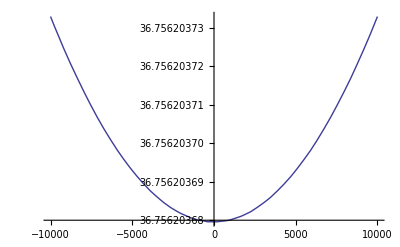

```mathematica
g =9.8;c=3*10^8;
Plot[Log[w[t]],{t,-10000,10000}]
```

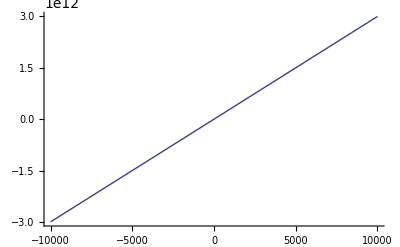

```mathematica
Show[Plot[w[t],{t,-10000,10000}],Plot[c*t,{t,-10000,10000}]]
```

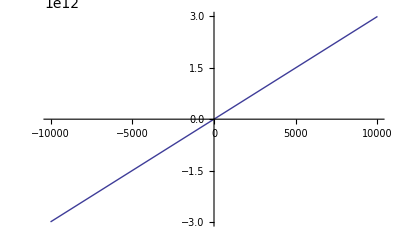

```mathematica
Plot[c*t,{t,-10000,10000}]
```

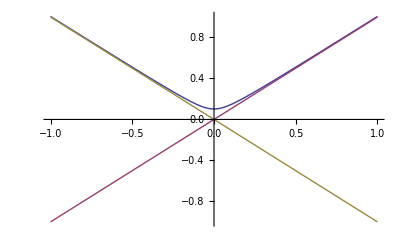

```mathematica
Plot[{w[t]/.{c->1,g->9.8},c*t/.{c->1},-c*t/.{c->1}},{t,-1,1}]
```

```mathematica
v[t_]=D[w[t],t]
```

(c^2 t)/(√(c^4/g^2+c^2 t^2))

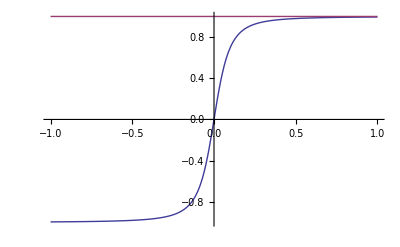

```mathematica
Plot[{v[t]/.{c->1,g->9.8},c/.{c->1}},{t,-1,1}]
```

```mathematica
a[t_] =D[v[t],t]
```

-(c^4 t^2)/((c^4/g^2+c^2 t^2)^(3/2))+c^2/(√(c^4/g^2+c^2 t^2))

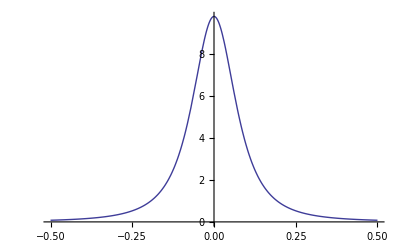

```mathematica
Plot[a[t]/.{c->1,g->9.8},{t,-.5,.5}]
```

```mathematica
e=1.60217662*10^-19;
R=1;
β[t_]=v[t]/c;
Manipulate[{PolarPlot[e/((1-β[t]*Cos[θ])*R),{θ,0,2*Pi}]},{t,0,1000,100}]
```

```mathematica
Animate[{PolarPlot[e/((1-β[t]*Cos[θ])*R),{θ,0,2*Pi}]},{t,0,10}]
```

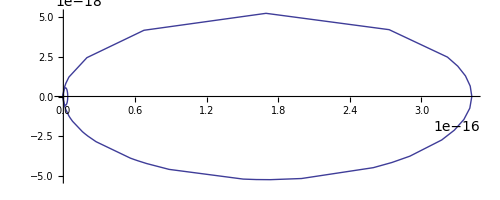

```mathematica
Show[PolarPlot[e/((1-β[0]*Cos[θ])*R),{θ,0,2*Pi}],PolarPlot[e/((1-β[100000000]*Cos[θ])*R),{θ,0,2*Pi}],PolarPlot[e/((1-β[1000000000]*Cos[θ])*R),{θ,0,2*Pi}]]
```

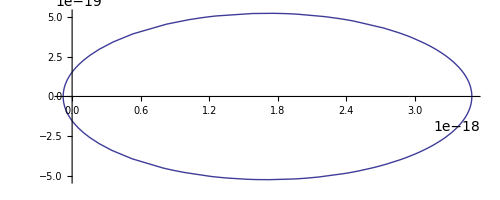

```mathematica
t=100000000;
PolarPlot[(e*β[t])/((1-β[t]*Cos[θ])*R),{θ,0,2*Pi}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
g =9.8;c=3*10^8;e=1.60217662*10^-19;
w[t_] = √((c^2/g)^2+(c*t)^2);
v[t_]=D[w[t],t];
β[t_]=v[t]/c;
ϕ[r_,θ_,t_] = e/((1-β[t]*Cos[θ])*r);
A[r_,θ_,t_]=(e*β[t])/((1-β[t]*Cos[θ])*r);
```

```mathematica
Elec[r,θ,t]=-1/c*D[A[r,θ,t],t]-(D[ϕ[r,θ,t],r]+1/r*D[ϕ[r,θ,t],θ])
```

(1.60218×10^-19)/(r^2 (1-(300000000 t Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2))))+1/300000000((4.80653×10^-11 t ((27000000000000000000000000 t^2 Cos[θ])/((8.43399×10^31+90000000000000000 t^2)^(3/2))-(300000000 Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2))))/(r √(8.43399×10^31+90000000000000000 t^2) (1-(300000000 t Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2)))^2)+(4.32588×10^6 t^2)/(r (8.43399×10^31+90000000000000000 t^2)^(3/2) (1-(300000000 t Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2))))-4.80653×10^-11/(r √(8.43399×10^31+90000000000000000 t^2) (1-(300000000 t Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2)))))+(4.80653×10^-11 t Sin[θ])/(r^2 √(8.43399×10^31+90000000000000000 t^2) (1-(300000000 t Cos[θ])/(√(8.43399×10^31+90000000000000000 t^2)))^2)

```mathematica
Elec[r,θ,t]/.{r->1,t->1}
PolarPlot[Elec[r,θ,t]/.{r->1,t->1},{θ,0,2*Pi}]
```

(1.60218×10^-19)/(1-3.26667×10^-8 Cos[θ])+(-(5.23378×10^-27)/(1-3.26667×10^-8 Cos[θ])-(1.7097×10^-34 Cos[θ])/((1-3.26667×10^-8 Cos[θ])^2))/300000000+(5.23378×10^-27 Sin[θ])/((1-3.26667×10^-8 Cos[θ])^2)

-Graphics-